### PARAMETRES

```mathematica
listH ={100,100,100} (*мощности слоев*)
alpha = 0 Degree (*наклон слоев*)
len = 1000(*длина профиля*)
dx = 5(*шаг по профилю*)
anoMaxDisp = 100(*степень складчатости нижнего слоя в метрах*)
hTapering =5  (*степень влияния нижнего горизонта на верхние*)
listV = {1000,2000,3000, 4000} (*набор скоростей*)
numOfWells = 10 (*кол скважин*)
wellsLocation = "min" (*расположение скважин "max","min","regular","random"*)
type = 1 (*выполаживание. 1 - кверху, -1 - книзу!!!*)
```

{100,100,100}

0

1000

5

100

5

{1000,2000,3000,4000}

10

min

1

### DEPTH

```mathematica
horNH = BuildDepthSection[listH,alpha,len,dx,anoMaxDisp,hTapering, type][["horNH"]]
```

{{{0,14},{5,19},{10,25},{15,31},{20,35},{25,41},{30,47},{35,52},{40,57},{45,62},{50,66},{55,71},{60,74},{65,79},{70,83},{75,85},{80,87},{85,88},{90,90},{95,91},{100,91},{105,91},{110,90},{115,89},{120,87},{125,85},{130,82},{135,80},{140,78},{145,73},{150,70},{155,65},{160,62},{165,59},{170,55},{175,52},{180,49},{185,48},{190,46},{195,44},{200,43},{205,41},{210,40},{215,40},{220,41},{225,41},{230,42},{235,44},{240,45},{245,48},{250,50},{255,53},{260,54},{265,57},{270,59},{275,60},{280,64},{285,67},{290,69},{295,71},{300,72},{305,73},{310,75},{315,76},{320,76},{325,76},{330,77},{335,79},{340,80},{345,79},{350,81},{355,83},{360,85},{365,85},{370,84},{375,85},{380,85},{385,87},{390,88},{395,88},{400,90},{405,91},{410,92},{415,93},{420,95},{425,95},{430,95},{435,96},{440,96},{445,95},{450,95},{455,93},{460,93},{465,94},{470,93},{475,93},{480,92},{485,90},{490,88},{495,88},{500,87},{505,86},{510,86},{515,85},{520,85},{525,85},{530,85},{535,85},{540,84},{545,84},{550,84},{555,83},{560,83},{565,83},{570,83},{575,84},{580,83},{585,83},{590,82},{595,81},{600,83},{605,82},{610,83},{615,83},{620,83},{625,84},{630,85},{635,87},{640,88},{645,90},{650,92},{655,95},{660,97},{665,99},{670,101},{675,104},{680,107},{685,109},{690,113},{695,116},{700,117},{705,119},{710,122},{715,123},{720,124},{725,123},{730,125},{735,125},{740,124},{745,123},{750,121},{755,120},{760,119},{765,116},{770,113},{775,111},{780,108},{785,105},{790,102},{795,100},{800,97},{805,94},{810,93},{815,91},{820,90},{825,90},{830,89},{835,90},{840,90},{845,91},{850,92},{855,93},{860,95},{865,97},{870,101},{875,102},{880,105},{885,106},{890,109},{895,111},{900,114},{905,118},{910,121},{915,124},{920,127},{925,131},{930,135},{935,137},{940,142},{945,146},{950,151},{955,156},{960,160},{965,166},{970,172},{975,178},{980,185},{985,192},{990,199},{995,206},{1000,213}},{{0,-121},{5,-114},{10,-105},{15,-99},{20,-91},{25,-83},{30,-76},{35,-67},{40,-59},{45,-52},{50,-45},{55,-39},{60,-34},{65,-29},{70,-25},{75,-22},{80,-21},{85,-20},{90,-19},{95,-20},{100,-20},{105,-20},{110,-23},{115,-26},{120,-30},{125,-32},{130,-34},{135,-38},{140,-43},{145,-47},{150,-49},{155,-53},{160,-58},{165,-62},{170,-67},{175,-72},{180,-78},{185,-83},{190,-89},{195,-94},{200,-98},{205,-103},{210,-104},{215,-107},{220,-107},{225,-106},{230,-104},{235,-101},{240,-97},{245,-90},{250,-82},{255,-74},{260,-67},{265,-59},{270,-52},{275,-46},{280,-40},{285,-37},{290,-34},{295,-34},{300,-35},{305,-37},{310,-41},{315,-43},{320,-45},{325,-48},{330,-51},{335,-54},{340,-56},{345,-57},{350,-55},{355,-55},{360,-54},{365,-52},{370,-47},{375,-43},{380,-40},{385,-37},{390,-33},{395,-29},{400,-27},{405,-26},{410,-24},{415,-23},{420,-22},{425,-20},{430,-20},{435,-19},{440,-20},{445,-21},{450,-24},{455,-25},{460,-26},{465,-29},{470,-30},{475,-32},{480,-36},{485,-38},{490,-40},{495,-41},{500,-42},{505,-44},{510,-45},{515,-44},{520,-45},{525,-47},{530,-45},{535,-43},{540,-42},{545,-40},{550,-39},{555,-38},{560,-37},{565,-36},{570,-36},{575,-36},{580,-36},{585,-37},{590,-39},{595,-39},{600,-40},{605,-42},{610,-43},{615,-44},{620,-46},{625,-47},{630,-48},{635,-48},{640,-48},{645,-48},{650,-46},{655,-45},{660,-41},{665,-37},{670,-33},{675,-27},{680,-23},{685,-17},{690,-10},{695,-4},{700,1},{705,8},{710,13},{715,17},{720,20},{725,23},{730,23},{735,22},{740,21},{745,18},{750,15},{755,10},{760,3},{765,-2},{770,-9},{775,-15},{780,-23},{785,-28},{790,-31},{795,-36},{800,-40},{805,-43},{810,-45},{815,-46},{820,-47},{825,-49},{830,-47},{835,-46},{840,-46},{845,-44},{850,-42},{855,-39},{860,-37},{865,-34},{870,-30},{875,-26},{880,-22},{885,-18},{890,-14},{895,-8},{900,-5},{905,1},{910,6},{915,9},{920,11},{925,11},{930,12},{935,14},{940,14},{945,15},{950,15},{955,16},{960,18},{965,20},{970,24},{975,29},{980,36},{985,45},{990,56},{995,68},{1000,81}},{{0,-241},{5,-233},{10,-227},{15,-218},{20,-208},{25,-198},{30,-190},{35,-181},{40,-173},{45,-166},{50,-158},{55,-151},{60,-145},{65,-139},{70,-136},{75,-132},{80,-132},{85,-129},{90,-129},{95,-131},{100,-133},{105,-136},{110,-139},{115,-141},{120,-144},{125,-149},{130,-154},{135,-156},{140,-159},{145,-161},{150,-163},{155,-168},{160,-173},{165,-176},{170,-181},{175,-186},{180,-193},{185,-198},{190,-204},{195,-211},{200,-217},{205,-224},{210,-229},{215,-232},{220,-236},{225,-237},{230,-235},{235,-231},{240,-224},{245,-216},{250,-207},{255,-196},{260,-183},{265,-170},{270,-159},{275,-149},{280,-141},{285,-137},{290,-137},{295,-138},{300,-139},{305,-145},{310,-151},{315,-159},{320,-167},{325,-175},{330,-179},{335,-180},{340,-182},{345,-182},{350,-181},{355,-177},{360,-172},{365,-167},{370,-163},{375,-160},{380,-155},{385,-150},{390,-147},{395,-144},{400,-143},{405,-140},{410,-137},{415,-136},{420,-136},{425,-135},{430,-134},{435,-135},{440,-135},{445,-136},{450,-136},{455,-139},{460,-141},{465,-145},{470,-147},{475,-148},{480,-151},{485,-153},{490,-157},{495,-160},{500,-161},{505,-165},{510,-168},{515,-167},{520,-166},{525,-164},{530,-163},{535,-161},{540,-160},{545,-157},{550,-153},{555,-153},{560,-149},{565,-148},{570,-148},{575,-150},{580,-151},{585,-151},{590,-155},{595,-157},{600,-157},{605,-160},{610,-159},{615,-161},{620,-164},{625,-164},{630,-165},{635,-168},{640,-168},{645,-168},{650,-168},{655,-166},{660,-163},{665,-161},{670,-157},{675,-151},{680,-144},{685,-136},{690,-128},{695,-119},{700,-113},{705,-104},{710,-97},{715,-94},{720,-87},{725,-84},{730,-82},{735,-83},{740,-83},{745,-88},{750,-95},{755,-102},{760,-109},{765,-117},{770,-126},{775,-136},{780,-143},{785,-150},{790,-156},{795,-162},{800,-165},{805,-165},{810,-167},{815,-167},{820,-165},{825,-166},{830,-164},{835,-164},{840,-163},{845,-162},{850,-159},{855,-158},{860,-156},{865,-154},{870,-152},{875,-147},{880,-143},{885,-138},{890,-132},{895,-125},{900,-118},{905,-114},{910,-109},{915,-104},{920,-98},{925,-94},{930,-93},{935,-95},{940,-96},{945,-100},{950,-104},{955,-106},{960,-108},{965,-110},{970,-108},{975,-105},{980,-97},{985,-87},{990,-75},{995,-59},{1000,-41}},{{0,-403},{5,-392},{10,-379},{15,-365},{20,-354},{25,-345},{30,-337},{35,-331},{40,-324},{45,-317},{50,-307},{55,-303},{60,-290},{65,-279},{70,-274},{75,-271},{80,-275},{85,-277},{90,-276},{95,-276},{100,-273},{105,-274},{110,-278},{115,-290},{120,-301},{125,-311},{130,-319},{135,-323},{140,-322},{145,-317},{150,-310},{155,-305},{160,-304},{165,-307},{170,-317},{175,-333},{180,-348},{185,-360},{190,-364},{195,-368},{200,-374},{205,-376},{210,-380},{215,-382},{220,-391},{225,-396},{230,-403},{235,-406},{240,-409},{245,-410},{250,-399},{255,-378},{260,-348},{265,-313},{270,-281},{275,-253},{280,-241},{285,-237},{290,-245},{295,-258},{300,-277},{305,-295},{310,-309},{315,-326},{320,-340},{325,-350},{330,-354},{335,-352},{340,-347},{345,-341},{350,-340},{355,-337},{360,-333},{365,-327},{370,-312},{375,-299},{380,-288},{385,-283},{390,-285},{395,-292},{400,-297},{405,-298},{410,-297},{415,-296},{420,-295},{425,-291},{430,-280},{435,-269},{440,-264},{445,-266},{450,-272},{455,-286},{460,-304},{465,-317},{470,-322},{475,-311},{480,-301},{485,-294},{490,-292},{495,-294},{500,-303},{505,-317},{510,-324},{515,-329},{520,-335},{525,-335},{530,-339},{535,-334},{540,-324},{545,-313},{550,-298},{555,-280},{560,-266},{565,-266},{570,-271},{575,-286},{580,-309},{585,-324},{590,-336},{595,-337},{600,-327},{605,-315},{610,-301},{615,-292},{620,-289},{625,-297},{630,-309},{635,-318},{640,-330},{645,-336},{650,-338},{655,-335},{660,-333},{665,-329},{670,-321},{675,-311},{680,-300},{685,-285},{690,-272},{695,-261},{700,-252},{705,-250},{710,-249},{715,-245},{720,-239},{725,-230},{730,-220},{735,-212},{740,-213},{745,-213},{750,-220},{755,-233},{760,-251},{765,-266},{770,-283},{775,-300},{780,-315},{785,-328},{790,-333},{795,-332},{800,-332},{805,-319},{810,-312},{815,-309},{820,-313},{825,-314},{830,-315},{835,-319},{840,-321},{845,-317},{850,-311},{855,-304},{860,-308},{865,-310},{870,-311},{875,-309},{880,-307},{885,-299},{890,-288},{895,-277},{900,-269},{905,-263},{910,-256},{915,-249},{920,-242},{925,-235},{930,-229},{935,-224},{940,-227},{945,-232},{950,-241},{955,-251},{960,-261},{965,-274},{970,-290},{975,-304},{980,-311},{985,-302},{990,-278},{995,-238},{1000,-194}}}

```mathematica
PlotDepthSection[horNH, Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
						PlotLabel -> "Depth Section"]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horNH,listV][["velModel"]]
datasetVelModel=BuildVelocitySection[horNH,listV][["datasetVelModel"]]
```

Dataset[<>]

```mathematica
PlotVelocity[velModel, horNH, {PlotStyle -> {Directive[Thickness[0.005], Black]},
							PlotLabel->"Velocity Distribution",
							PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
							ImageSize -> 500, 
ColorFunction -> ColorData[{"RedBlueTones", "Reverse"}],
						PlotLegends -> BarLegend[Automatic, LegendLabel -> "Vel, m/s"],
						PlotLabel -> "Velocity Distribution",
						Contours -> {Automatic, 10}}]
```

-Graphics-

### TIME

```mathematica
timeNH=BuildTimeSection[horNH, velModel][["timeNH"]]
```

{{{0,0},{5,0},{10,0},{15,0},{20,0},{25,0},{30,0},{35,0},{40,0},{45,0},{50,0},{55,0},{60,0},{65,0},{70,0},{75,0},{80,0},{85,0},{90,0},{95,0},{100,0},{105,0},{110,0},{115,0},{120,0},{125,0},{130,0},{135,0},{140,0},{145,0},{150,0},{155,0},{160,0},{165,0},{170,0},{175,0},{180,0},{185,0},{190,0},{195,0},{200,0},{205,0},{210,0},{215,0},{220,0},{225,0},{230,0},{235,0},{240,0},{245,0},{250,0},{255,0},{260,0},{265,0},{270,0},{275,0},{280,0},{285,0},{290,0},{295,0},{300,0},{305,0},{310,0},{315,0},{320,0},{325,0},{330,0},{335,0},{340,0},{345,0},{350,0},{355,0},{360,0},{365,0},{370,0},{375,0},{380,0},{385,0},{390,0},{395,0},{400,0},{405,0},{410,0},{415,0},{420,0},{425,0},{430,0},{435,0},{440,0},{445,0},{450,0},{455,0},{460,0},{465,0},{470,0},{475,0},{480,0},{485,0},{490,0},{495,0},{500,0},{505,0},{510,0},{515,0},{520,0},{525,0},{530,0},{535,0},{540,0},{545,0},{550,0},{555,0},{560,0},{565,0},{570,0},{575,0},{580,0},{585,0},{590,0},{595,0},{600,0},{605,0},{610,0},{615,0},{620,0},{625,0},{630,0},{635,0},{640,0},{645,0},{650,0},{655,0},{660,0},{665,0},{670,0},{675,0},{680,0},{685,0},{690,0},{695,0},{700,0},{705,0},{710,0},{715,0},{720,0},{725,0},{730,0},{735,0},{740,0},{745,0},{750,0},{755,0},{760,0},{765,0},{770,0},{775,0},{780,0},{785,0},{790,0},{795,0},{800,0},{805,0},{810,0},{815,0},{820,0},{825,0},{830,0},{835,0},{840,0},{845,0},{850,0},{855,0},{860,0},{865,0},{870,0},{875,0},{880,0},{885,0},{890,0},{895,0},{900,0},{905,0},{910,0},{915,0},{920,0},{925,0},{930,0},{935,0},{940,0},{945,0},{950,0},{955,0},{960,0},{965,0},{970,0},{975,0},{980,0},{985,0},{990,0},{995,0},{1000,0}},{{0,0.10445},{5,0.105192},{10,0.105217},{15,0.107863},{20,0.10705},{25,0.108298},{30,0.110215},{35,0.109692},{40,0.110005},{45,0.110893},{50,0.110903},{55,0.112468},{60,0.112705},{65,0.115023},{70,0.116646},{75,0.117032},{80,0.118425},{85,0.118931},{90,0.120352},{95,0.121887},{100,0.121783},{105,0.12172},{110,0.122403},{115,0.122986},{120,0.123283},{125,0.122449},{130,0.120499},{135,0.120802},{140,0.121765},{145,0.119197},{150,0.117281},{155,0.114493},{160,0.114504},{165,0.113829},{170,0.112824},{175,0.112899},{180,0.113508},{185,0.115649},{190,0.117473},{195,0.11853},{200,0.119987},{205,0.121052},{210,0.120302},{215,0.122272},{220,0.122983},{225,0.122168},{230,0.121849},{235,0.122111},{240,0.120721},{245,0.119408},{250,0.116463},{255,0.114691},{260,0.111758},{265,0.110116},{270,0.108079},{275,0.105627},{280,0.106257},{285,0.107648},{290,0.10784},{295,0.109849},{300,0.111482},{305,0.113575},{310,0.117758},{315,0.119684},{320,0.120721},{325,0.122221},{330,0.124921},{335,0.128717},{340,0.130906},{345,0.130518},{350,0.131266},{355,0.133424},{360,0.134924},{365,0.133854},{370,0.129962},{375,0.128606},{380,0.126982},{385,0.127295},{390,0.125982},{395,0.12373},{400,0.124557},{405,0.125125},{410,0.124958},{415,0.125408},{420,0.126749},{425,0.125647},{430,0.12569},{435,0.126113},{440,0.12665},{445,0.126136},{450,0.127827},{455,0.126402},{460,0.126953},{465,0.12951},{470,0.129074},{475,0.130218},{480,0.131512},{485,0.130703},{490,0.129824},{495,0.13035},{500,0.129951},{505,0.129999},{510,0.130547},{515,0.128957},{520,0.129608},{525,0.130969},{530,0.129715},{535,0.128668},{540,0.127015},{545,0.125915},{550,0.125499},{555,0.12383},{560,0.123441},{565,0.122806},{570,0.122836},{575,0.123741},{580,0.12278},{585,0.123329},{590,0.123459},{595,0.122384},{600,0.124927},{605,0.125046},{610,0.126733},{615,0.127235},{620,0.128293},{625,0.129938},{630,0.131481},{635,0.133308},{640,0.134303},{645,0.136167},{650,0.13691},{655,0.139285},{660,0.138849},{665,0.138447},{670,0.138164},{675,0.137736},{680,0.138548},{685,0.137306},{690,0.137383},{695,0.137189},{700,0.13708},{705,0.145846},{710,0.153662},{715,0.15864},{720,0.162579},{725,0.1649},{730,0.166755},{735,0.165678},{740,0.163804},{745,0.159744},{750,0.154801},{755,0.148846},{760,0.1409},{765,0.136133},{770,0.136934},{775,0.138102},{780,0.139493},{785,0.139284},{790,0.138091},{795,0.138832},{800,0.138272},{805,0.137118},{810,0.137343},{815,0.135991},{820,0.135694},{825,0.136889},{830,0.134778},{835,0.135125},{840,0.13519},{845,0.134945},{850,0.134841},{855,0.134014},{860,0.134752},{865,0.135087},{870,0.136634},{875,0.135382},{880,0.136181},{885,0.135004},{890,0.135718},{895,0.134587},{900,0.135851},{905,0.13802},{910,0.145708},{915,0.151306},{920,0.156142},{925,0.159723},{930,0.164391},{935,0.168015},{940,0.172456},{945,0.176894},{950,0.181131},{955,0.186341},{960,0.191595},{965,0.198539},{970,0.207411},{975,0.217356},{980,0.230297},{985,0.245177},{990,0.262225},{995,0.280665},{1000,0.300778}},{{0,0.229698},{5,0.226613},{10,0.224046},{15,0.222394},{20,0.216452},{25,0.212314},{30,0.210039},{35,0.204623},{40,0.200602},{45,0.197852},{50,0.193797},{55,0.191476},{60,0.188989},{65,0.188409},{70,0.188578},{75,0.186816},{80,0.187987},{85,0.186617},{90,0.188145},{95,0.19083},{100,0.192039},{105,0.193674},{110,0.195813},{115,0.196975},{120,0.198391},{125,0.199915},{130,0.200438},{135,0.201608},{140,0.204409},{145,0.203267},{150,0.202909},{155,0.203391},{160,0.206514},{165,0.207439},{170,0.208693},{175,0.210597},{180,0.214357},{185,0.218571},{190,0.223686},{195,0.228664},{200,0.233203},{205,0.238298},{210,0.240276},{215,0.243876},{220,0.246287},{225,0.245567},{230,0.243477},{235,0.241211},{240,0.235356},{245,0.229412},{250,0.222002},{255,0.215297},{260,0.206657},{265,0.199695},{270,0.19321},{275,0.186628},{280,0.18319},{285,0.182402},{290,0.182055},{295,0.18386},{300,0.184963},{305,0.189606},{310,0.196475},{315,0.202055},{320,0.206927},{325,0.212408},{330,0.217212},{335,0.221664},{340,0.225351},{345,0.22532},{350,0.225565},{355,0.22556},{360,0.224381},{365,0.220805},{370,0.215457},{375,0.213198},{380,0.209248},{385,0.206939},{390,0.203723},{395,0.199352},{400,0.199278},{405,0.198125},{410,0.19629},{415,0.196197},{420,0.19762},{425,0.196156},{430,0.196178},{435,0.197717},{440,0.198532},{445,0.198518},{450,0.199864},{455,0.199444},{460,0.200163},{465,0.204344},{470,0.204815},{475,0.207153},{480,0.210663},{485,0.211447},{490,0.21304},{495,0.215227},{500,0.214823},{505,0.216327},{510,0.218226},{515,0.21582},{520,0.215521},{525,0.215721},{530,0.213665},{535,0.211762},{540,0.210095},{545,0.207912},{550,0.206007},{555,0.205345},{560,0.203523},{565,0.202305},{570,0.202051},{575,0.203253},{580,0.201496},{585,0.201194},{590,0.20308},{595,0.203046},{600,0.206142},{605,0.208581},{610,0.210639},{615,0.212862},{620,0.215872},{625,0.217025},{630,0.218344},{635,0.221307},{640,0.221611},{645,0.223087},{650,0.223831},{655,0.225222},{660,0.223157},{665,0.221802},{670,0.219711},{675,0.21636},{680,0.213762},{685,0.208684},{690,0.204784},{695,0.199975},{700,0.196815},{705,0.20051},{710,0.20445},{715,0.207893},{720,0.208111},{725,0.209055},{730,0.210123},{735,0.209847},{740,0.207954},{745,0.20675},{750,0.20559},{755,0.203076},{760,0.198385},{765,0.19752},{770,0.20271},{775,0.208716},{780,0.213331},{785,0.216414},{790,0.218378},{795,0.222611},{800,0.223762},{805,0.223397},{810,0.225255},{815,0.224017},{820,0.222287},{825,0.223998},{830,0.220693},{835,0.220758},{840,0.220143},{845,0.219548},{850,0.218073},{855,0.217067},{860,0.216406},{865,0.215525},{870,0.215811},{875,0.211816},{880,0.210431},{885,0.206825},{890,0.204639},{895,0.200037},{900,0.19772},{905,0.197819},{910,0.202988},{915,0.206017},{920,0.207762},{925,0.209324},{930,0.213655},{935,0.218598},{940,0.22352},{945,0.230027},{950,0.236181},{955,0.242139},{960,0.248094},{965,0.255691},{970,0.262846},{975,0.270656},{980,0.279131},{985,0.288947},{990,0.300222},{995,0.311004},{1000,0.322232}},{{0,0.423014},{5,0.409741},{10,0.39726},{15,0.386568},{20,0.373823},{25,0.364381},{30,0.357543},{35,0.348702},{40,0.341012},{45,0.334325},{50,0.325039},{55,0.320674},{60,0.311632},{65,0.305524},{70,0.303294},{75,0.299999},{80,0.303229},{85,0.302724},{90,0.303716},{95,0.306438},{100,0.306222},{105,0.308409},{110,0.312476},{115,0.319616},{120,0.326552},{125,0.333263},{130,0.337994},{135,0.341294},{140,0.343437},{145,0.339899},{150,0.335683},{155,0.333636},{160,0.336172},{165,0.338696},{170,0.345045},{175,0.355881},{180,0.367932},{185,0.379497},{190,0.386979},{195,0.394662},{200,0.403015},{205,0.409651},{210,0.414302},{215,0.419577},{220,0.428612},{225,0.432038},{230,0.435606},{235,0.437734},{240,0.435847},{245,0.432132},{250,0.410933},{255,0.387913},{260,0.360324},{265,0.334072},{270,0.311209},{275,0.291286},{280,0.282223},{285,0.279665},{290,0.282972},{295,0.290872},{300,0.301083},{305,0.314708},{310,0.328832},{315,0.343275},{320,0.355993},{325,0.367196},{330,0.374615},{335,0.377825},{340,0.378666},{345,0.374937},{350,0.374661},{355,0.373105},{360,0.369579},{365,0.362735},{370,0.349372},{375,0.340354},{380,0.330873},{385,0.326008},{390,0.323754},{395,0.32292},{400,0.325402},{405,0.324843},{410,0.322446},{415,0.321819},{420,0.322735},{425,0.319257},{430,0.313749},{435,0.309978},{440,0.30836},{445,0.309262},{450,0.31368},{455,0.320006},{460,0.329795},{465,0.340918},{470,0.343948},{475,0.340537},{480,0.338855},{485,0.335998},{490,0.336708},{495,0.339794},{500,0.344042},{505,0.352842},{510,0.358605},{515,0.35871},{520,0.361867},{525,0.362044},{530,0.3623},{535,0.357566},{540,0.350397},{545,0.342347},{550,0.332717},{555,0.322939},{560,0.314319},{565,0.313079},{570,0.315317},{575,0.323886},{580,0.333833},{585,0.341505},{590,0.350014},{595,0.350552},{600,0.34802},{605,0.343912},{610,0.338739},{615,0.3364},{620,0.337891},{625,0.343106},{630,0.350779},{635,0.358351},{640,0.365163},{645,0.370076},{650,0.371841},{655,0.371532},{660,0.368284},{665,0.364814},{670,0.358227},{675,0.349661},{680,0.34146},{685,0.328781},{690,0.318508},{695,0.308334},{700,0.301005},{705,0.303771},{710,0.307228},{715,0.308734},{720,0.306188},{725,0.303012},{730,0.299542},{735,0.295713},{740,0.294255},{745,0.293038},{750,0.294992},{755,0.298415},{760,0.301987},{765,0.308295},{770,0.321824},{775,0.336297},{780,0.348631},{785,0.358811},{790,0.363696},{795,0.367307},{800,0.368366},{805,0.360908},{810,0.359153},{815,0.356369},{820,0.356668},{825,0.358873},{830,0.356119},{835,0.358339},{840,0.358809},{845,0.356011},{850,0.351484},{855,0.346724},{860,0.348145},{865,0.34846},{870,0.349164},{875,0.344271},{880,0.341641},{885,0.333872},{890,0.326179},{895,0.316176},{900,0.310024},{905,0.30722},{910,0.309019},{915,0.30872},{920,0.307232},{925,0.305566},{930,0.307178},{935,0.309813},{940,0.316056},{945,0.324943},{950,0.33522},{955,0.345823},{960,0.356496},{965,0.370298},{970,0.385421},{975,0.400311},{980,0.412501},{985,0.417618},{990,0.416897},{995,0.408601},{1000,0.400091}}}

```mathematica
PlotTimeSection[timeNH, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[timeNH]] - 1)],
						PlotLabel -> "Time Section"}]
```

-Graphics-

### WELLS

```mathematica
datasetWells=BuildWellSet[horNH,timeNH, numOfWells, wellsLocation][["datasetWells"]]
```

```mathematica
PlotDepthSection[horNH, datasetWells,{GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
											Filling -> Bottom, Frame -> True, ImageSize -> 500,
											PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[timeNH, {GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[timeNH]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### Vint

```mathematica
listVint = CheckVelocity[datasetWells][["datasetVint"]]
```

### HT

```mathematica
Clear[t]

dataWellsHT=HT[datasetWells,timeNH, t][["dataWellsHT"]]
lmSetHT=HT[datasetWells,timeNH, t][["lmSet"]]
fitsHTParams=HT[datasetWells, timeNH, t][["fitsHTParams"]]
resultHT=HT[datasetWells, timeNH, t][["resultHT"]]
wellsSet = HT[datasetWells, timeNH, t][["wellsSet"]]
htSet = HT[datasetWells, timeNH, t][["htSet"]]
interpolationErrors= HT[datasetWells, timeNH, t][["interpolationErrors"]]
```

{{{0.10445,-121.},{0.120802,-38.},{0.119408,-90.},{0.124921,-51.},{0.129074,-30.},{0.129715,-45.},{0.13691,-46.},{0.138091,-31.},{0.13519,-46.},{0.230297,36.}},{{0.229698,-241.},{0.201608,-156.},{0.229412,-216.},{0.217212,-179.},{0.204815,-147.},{0.213665,-163.},{0.223831,-168.},{0.218378,-156.},{0.220143,-163.},{0.279131,-97.}},{{0.423014,-403.},{0.341294,-323.},{0.432132,-410.},{0.374615,-354.},{0.343948,-322.},{0.3623,-339.},{0.371841,-338.},{0.363696,-333.},{0.358809,-321.},{0.412501,-311.}}}

{FittedModel[-184.075+1007.23 t],FittedModel[-302.883+600.043 t],FittedModel[-55.8676-765.119 t]}

{{-184.075,1007.23},{-302.883,600.043},{-55.8676,-765.119}}

{{{0,14.},{135,80.},{245,48.},{330,77.},{470,93.},{530,85.},{650,92.},{790,102.},{840,90.},{980,185.}},{{0,-121.},{5,-109.784},{10,-100.126},{15,-88.6366},{20,-81.4141},{25,-72.8714},{30,-64.3842},{35,-59.0584},{40,-53.568},{45,-48.1488},{50,-44.2389},{55,-39.3616},{60,-36.3926},{65,-31.8732},{70,-28.5737},{75,-27.0122},{80,-24.9027},{85,-24.1278},{90,-22.8439},{95,-21.8338},{100,-22.8354},{105,-24.1299},{110,-24.9822},{115,-26.2163},{120,-27.9949},{125,-31.1432},{130,-35.6178},{135,-38.},{140,-39.8679},{145,-45.4164},{150,-50.4061},{155,-56.3454},{160,-59.5102},{165,-63.3857},{170,-67.5855},{175,-70.6638},{180,-73.1444},{185,-73.9951},{190,-75.052},{195,-76.7423},{200,-77.8646},{205,-79.19},{210,-82.1249},{215,-82.0755},{220,-83.024},{225,-85.2118},{230,-86.5767},{235,-87.0066},{240,-88.7261},{245,-90.},{250,-92.5738},{255,-93.6473},{260,-95.5942},{265,-95.9702},{270,-96.4985},{275,-97.2235},{280,-94.6478},{285,-91.132},{290,-88.6773},{295,-84.2685},{300,-80.1396},{305,-75.4734},{310,-68.6525},{315,-64.0795},{320,-60.401},{325,-56.2807},{330,-51.},{335,-44.6883},{340,-40.0928},{345,-38.2146},{350,-35.3381},{355,-31.203},{360,-27.8909},{365,-27.3252},{370,-29.7569},{375,-29.7876},{380,-30.2405},{385,-28.8908},{390,-29.3248},{395,-30.8506},{400,-29.4165},{405,-28.3845},{410,-28.2304},{415,-27.5908},{420,-26.187},{425,-27.3753},{430,-27.5406},{435,-27.4493},{440,-27.3686},{445,-28.469},{450,-27.4658},{455,-29.7101},{460,-30.0621},{465,-28.4835},{470,-30.},{475,-29.994},{480,-29.8975},{485,-31.9711},{490,-34.1554},{495,-34.9572},{500,-36.7129},{505,-38.0306},{510,-38.8475},{515,-41.8115},{520,-42.5025},{525,-42.452},{530,-45.},{535,-47.2957},{540,-50.1459},{545,-52.3754},{550,-53.8425},{555,-56.4907},{560,-57.7654},{565,-59.2059},{570,-59.8921},{575,-59.6152},{580,-61.1351},{585,-61.0514},{590,-61.3074},{595,-62.6946},{600,-60.3548},{605,-60.3742},{610,-58.7333},{615,-58.2031},{620,-57.0305},{625,-55.1856},{630,-53.3617},{635,-51.1702},{640,-49.735},{645,-47.3433},{650,-46.},{655,-42.9307},{660,-42.6127},{665,-42.1869},{670,-41.58},{675,-41.0691},{680,-39.2695},{685,-39.5122},{690,-38.4114},{695,-37.5784},{700,-36.6682},{705,-26.8382},{710,-17.9945},{715,-12.0523},{720,-7.21012},{725,-4.06223},{730,-1.46184},{735,-1.90159},{740,-3.24496},{745,-6.9012},{750,-11.5701},{755,-17.3927},{760,-25.367},{765,-30.2932},{770,-29.7607},{775,-28.9971},{780,-28.1414},{785,-29.018},{790,-31.},{795,-31.1381},{800,-32.6823},{805,-34.9108},{810,-35.8291},{815,-38.4037},{820,-39.9759},{825,-40.0971},{830,-43.5901},{835,-44.641},{840,-46.},{845,-47.6868},{850,-49.2378},{855,-51.5156},{860,-52.206},{865,-53.2826},{870,-53.1096},{875,-55.7183},{880,-56.2149},{885,-58.6451},{890,-59.1072},{895,-61.3549},{900,-61.1076},{905,-59.859},{910,-52.9511},{915,-48.0386},{920,-43.7779},{925,-40.6535},{930,-36.2993},{935,-32.8525},{940,-28.4299},{945,-23.8488},{950,-19.2985},{955,-13.5892},{960,-7.64616},{965,0.195373},{970,10.1852},{975,21.4718},{980,36.},{985,52.7132},{990,71.8528},{995,92.6443}},{{0,-241.},{5,-227.342},{10,-214.593},{15,-202.474},{20,-194.073},{25,-185.695},{30,-177.266},{35,-171.751},{40,-166.39},{45,-161.219},{50,-157.748},{55,-154.113},{60,-151.418},{65,-148.38},{70,-145.656},{75,-144.816},{80,-142.906},{85,-143.169},{90,-142.306},{95,-141.323},{100,-141.761},{105,-142.443},{110,-143.282},{115,-145.131},{120,-147.211},{125,-149.573},{130,-152.845},{135,-156.},{140,-158.409},{145,-163.378},{150,-168.034},{155,-172.306},{160,-175.075},{165,-179.205},{170,-183.144},{175,-186.66},{180,-188.991},{185,-190.943},{190,-192.207},{195,-193.37},{200,-194.573},{205,-195.184},{210,-197.366},{215,-198.24},{220,-199.453},{225,-202.134},{230,-205.187},{235,-207.858},{240,-212.161},{245,-216.},{250,-220.233},{255,-223.588},{260,-227.68},{265,-230.373},{270,-232.418},{275,-234.191},{280,-233.778},{285,-231.506},{290,-228.734},{295,-224.464},{300,-220.441},{305,-214.151},{310,-206.412},{315,-199.365},{320,-192.694},{325,-185.637},{330,-179.},{335,-172.617},{340,-166.768},{345,-163.255},{350,-159.713},{355,-156.479},{360,-154.113},{365,-153.352},{370,-153.824},{375,-152.619},{380,-152.606},{385,-151.793},{390,-151.71},{395,-152.511},{400,-150.929},{405,-150.193},{410,-150.069},{415,-149.107},{420,-147.446},{425,-147.733},{430,-147.346},{435,-146.273},{440,-145.86},{445,-146.176},{450,-145.903},{455,-146.899},{460,-147.406},{465,-146.01},{470,-147.},{475,-147.01},{480,-146.441},{485,-147.614},{490,-148.39},{495,-148.882},{500,-150.983},{505,-151.976},{510,-152.752},{515,-156.113},{520,-158.195},{525,-159.945},{530,-163.},{535,-165.896},{540,-168.566},{545,-171.444},{550,-174.036},{555,-175.749},{560,-178.025},{565,-179.81},{570,-180.888},{575,-180.97},{580,-182.706},{585,-183.453},{590,-182.772},{595,-183.132},{600,-181.507},{605,-180.172},{610,-178.964},{615,-177.559},{620,-175.587},{625,-174.637},{630,-173.5},{635,-171.29},{640,-170.593},{645,-169.115},{650,-168.},{655,-166.424},{660,-166.853},{665,-166.794},{670,-167.126},{675,-168.172},{680,-168.735},{685,-170.766},{690,-172.079},{695,-173.936},{700,-174.814},{705,-171.598},{710,-168.265},{715,-165.271},{720,-164.261},{725,-162.877},{730,-161.488},{735,-160.987},{740,-161.546},{745,-161.794},{750,-162.126},{755,-163.391},{760,-166.095},{765,-166.641},{770,-163.685},{775,-160.358},{780,-157.975},{785,-156.608},{790,-156.},{795,-154.106},{800,-154.127},{805,-155.111},{810,-154.803},{815,-156.385},{820,-158.283},{825,-158.127},{830,-160.979},{835,-161.797},{840,-163.},{845,-164.157},{850,-165.796},{855,-167.099},{860,-168.127},{865,-169.21},{870,-169.503},{875,-172.265},{880,-173.35},{885,-175.645},{890,-176.956},{895,-179.572},{900,-180.664},{905,-180.139},{910,-176.394},{915,-173.747},{920,-171.671},{925,-169.495},{930,-165.438},{935,-160.78},{940,-155.893},{945,-149.801},{950,-143.657},{955,-137.354},{960,-130.766},{965,-122.896},{970,-114.982},{975,-106.356},{980,-97.},{985,-86.4978},{990,-74.7675},{995,-62.9698}},{{0,-403.},{5,-389.629},{10,-377.134},{15,-366.27},{20,-354.086},{25,-344.674},{30,-337.489},{35,-328.998},{40,-321.605},{45,-315.189},{50,-306.985},{55,-302.738},{60,-295.095},{65,-289.872},{70,-287.781},{75,-285.033},{80,-287.426},{85,-287.1},{90,-288.051},{95,-290.448},{100,-290.711},{105,-292.918},{110,-296.66},{115,-302.84},{120,-308.943},{125,-314.945},{130,-319.493},{135,-323.},{140,-325.666},{145,-324.021},{150,-321.884},{155,-321.425},{160,-324.483},{165,-327.532},{170,-333.501},{175,-342.886},{180,-353.176},{185,-363.06},{190,-369.779},{195,-376.6},{200,-383.874},{205,-389.766},{210,-394.062},{215,-398.75},{220,-406.221},{225,-409.298},{230,-412.371},{235,-414.223},{240,-412.874},{245,-410.},{250,-393.631},{255,-375.758},{260,-354.288},{265,-333.746},{270,-315.712},{275,-299.85},{280,-292.227},{285,-289.52},{290,-291.248},{295,-296.444},{300,-303.371},{305,-312.882},{310,-322.754},{315,-332.857},{320,-341.636},{325,-349.26},{330,-354.},{335,-355.54},{340,-355.295},{345,-351.59},{350,-350.571},{355,-348.622},{360,-345.215},{365,-339.32},{370,-328.485},{375,-321.023},{380,-313.256},{385,-309.07},{390,-306.929},{395,-305.923},{400,-307.502},{405,-306.802},{410,-304.743},{415,-304.086},{420,-304.657},{425,-301.912},{430,-297.661},{435,-294.785},{440,-293.604},{445,-294.397},{450,-297.923},{455,-302.948},{460,-310.657},{465,-319.413},{470,-322.},{475,-319.675},{480,-318.685},{485,-316.8},{490,-317.646},{495,-320.305},{500,-323.842},{505,-330.846},{510,-335.504},{515,-335.806},{520,-338.411},{525,-338.697},{530,-339.},{535,-335.436},{540,-329.955},{545,-323.74},{550,-316.25},{555,-308.579},{560,-301.729},{565,-300.468},{570,-301.818},{575,-307.968},{580,-315.136},{585,-320.534},{590,-326.548},{595,-326.448},{600,-323.99},{605,-320.323},{610,-315.846},{615,-313.548},{620,-314.199},{625,-317.725},{630,-323.163},{635,-328.561},{640,-333.425},{645,-336.887},{650,-338.},{655,-337.592},{660,-335.008},{665,-332.325},{670,-327.32},{675,-320.856},{680,-314.721},{685,-305.202},{690,-297.558},{695,-290.017},{700,-284.674},{705,-287.068},{710,-289.996},{715,-291.431},{720,-289.756},{725,-287.584},{730,-285.165},{735,-282.441},{740,-281.495},{745,-280.688},{750,-282.258},{755,-284.892},{760,-287.574},{765,-292.279},{770,-302.437},{775,-313.246},{780,-322.348},{785,-329.734},{790,-333.},{795,-335.224},{800,-335.43},{805,-329.052},{810,-326.975},{815,-324.046},{820,-323.414},{825,-324.179},{830,-321.088},{835,-321.743},{840,-321.},{845,-317.699},{850,-313.017},{855,-308.101},{860,-307.859},{865,-306.717},{870,-305.818},{875,-300.586},{880,-297.032},{885,-289.496},{890,-281.969},{895,-272.624},{900,-266.179},{905,-262.248},{910,-261.793},{915,-259.687},{920,-256.628},{925,-253.389},{930,-252.616},{935,-252.583},{940,-255.271},{945,-259.942},{950,-265.638},{955,-271.545},{960,-277.47},{965,-285.752},{970,-295.009},{975,-304.054},{980,-311.},{985,-312.502},{990,-309.506},{995,-300.684}}}

{{-121.,-38.,-90.,-51.,-30.,-45.,-46.,-31.,-46.,36.},{-241.,-156.,-216.,-179.,-147.,-163.,-168.,-156.,-163.,-97.},{-403.,-323.,-410.,-354.,-322.,-339.,-338.,-333.,-321.,-311.}}

{{-78.87,-62.4004,-63.8038,-58.2513,-54.0686,-53.4222,-46.1759,-44.9859,-47.9084,47.8866},{-165.055,-181.91,-165.226,-172.547,-179.985,-174.675,-168.575,-171.847,-170.788,-135.393},{-379.524,-316.998,-386.5,-342.492,-319.029,-333.07,-340.37,-334.138,-330.399,-371.48}}

{{{0,-42.13},{5,-31.6617},{10,-22.0285},{15,-13.2042},{20,-5.16231},{25,2.12339},{30,8.67928},{35,14.5317},{40,19.7069},{45,24.2313},{50,28.1312},{55,31.433},{60,34.1629},{65,36.3474},{70,38.0127},{75,39.1852},{80,39.8912},{85,40.157},{90,40.009},{95,39.4736},{100,38.577},{105,37.3455},{110,35.8056},{115,33.9835},{120,31.9056},{125,29.5982},{130,27.0877},{135,24.4004},{140,21.5625},{145,18.6006},{150,15.5408},{155,12.4095},{160,9.23304},{165,6.03779},{170,2.85006},{175,-0.303825},{180,-3.39752},{185,-6.4047},{190,-9.29902},{195,-12.0542},{200,-14.6438},{205,-17.0416},{210,-19.2211},{215,-21.1562},{220,-22.8204},{225,-24.1874},{230,-25.2309},{235,-25.9246},{240,-26.2445},{245,-26.1962},{250,-25.8038},{255,-25.0919},{260,-24.0849},{265,-22.8074},{270,-21.284},{275,-19.5392},{280,-17.5975},{285,-15.4834},{290,-13.2215},{295,-10.8364},{300,-8.35243},{305,-5.79427},{310,-3.18641},{315,-0.553386},{320,2.08027},{325,4.69002},{330,7.25133},{335,9.73969},{340,12.1305},{345,14.3994},{350,16.5218},{355,18.4834},{360,20.2849},{365,21.9287},{370,23.4169},{375,24.7516},{380,25.9352},{385,26.9697},{390,27.8574},{395,28.6004},{400,29.2011},{405,29.6614},{410,29.9837},{415,30.1702},{420,30.223},{425,30.1443},{430,29.9363},{435,29.6013},{440,29.1413},{445,28.5587},{450,27.8584},{455,27.0497},{460,26.1421},{465,25.1452},{470,24.0686},{475,22.9219},{480,21.7147},{485,20.4565},{490,19.157},{495,17.8257},{500,16.4722},{505,15.1061},{510,13.737},{515,12.3745},{520,11.0282},{525,9.70753},{530,8.42223},{535,7.18186},{540,5.99598},{545,4.87418},{550,3.82606},{555,2.85958},{560,1.97625},{565,1.17597},{570,0.458626},{575,-0.175876},{580,-0.727645},{585,-1.19679},{590,-1.5834},{595,-1.8876},{600,-2.10948},{605,-2.24915},{610,-2.30672},{615,-2.28229},{620,-2.17596},{625,-1.98784},{630,-1.71804},{635,-1.36665},{640,-0.93379},{645,-0.419555},{650,0.175948},{655,0.852614},{660,1.60977},{665,2.44018},{670,3.33237},{675,4.27479},{680,5.25588},{685,6.2641},{690,7.2879},{695,8.31573},{700,9.33604},{705,10.3373},{710,11.3079},{715,12.2364},{720,13.1111},{725,13.9206},{730,14.6533},{735,15.2976},{740,15.8421},{745,16.275},{750,16.585},{755,16.7604},{760,16.7897},{765,16.6647},{770,16.391},{775,15.9774},{780,15.4327},{785,14.766},{790,13.9859},{795,13.1014},{800,12.1215},{805,11.0549},{810,9.91051},{815,8.69726},{820,7.424},{825,6.09962},{830,4.73297},{835,3.33295},{840,1.90842},{845,0.468276},{850,-0.978622},{855,-2.42339},{860,-3.85715},{865,-5.27104},{870,-6.65616},{875,-8.00365},{880,-9.30462},{885,-10.5502},{890,-11.7315},{895,-12.8397},{900,-13.8659},{905,-14.8011},{910,-15.6366},{915,-16.3635},{920,-16.9728},{925,-17.4557},{930,-17.8034},{935,-18.0068},{940,-18.0573},{945,-17.9458},{950,-17.6636},{955,-17.2017},{960,-16.5513},{965,-15.7034},{970,-14.6493},{975,-13.3799},{980,-11.8866},{985,-10.1603},{990,-8.1922},{995,-5.97344}},{{0,-75.9454},{5,-60.4365},{10,-46.1463},{15,-33.0371},{20,-21.0707},{25,-10.2094},{30,-0.415185},{35,8.34982},{40,16.1236},{45,22.9439},{50,28.8488},{55,33.8762},{60,38.064},{65,41.4501},{70,44.0724},{75,45.9688},{80,47.1773},{85,47.7357},{90,47.682},{95,47.0542},{100,45.89},{105,44.2275},{110,42.1045},{115,39.559},{120,36.6288},{125,33.352},{130,29.7664},{135,25.9099},{140,21.8204},{145,17.5359},{150,13.0943},{155,8.53351},{160,3.8914},{165,-0.794078},{170,-5.48501},{175,-10.1435},{180,-14.7316},{185,-19.2114},{190,-23.545},{195,-27.6945},{200,-31.6219},{205,-35.2894},{210,-38.659},{215,-41.6928},{220,-44.3529},{225,-46.6014},{230,-48.4003},{235,-49.7118},{240,-50.5014},{245,-50.7741},{250,-50.5607},{255,-49.8924},{260,-48.8002},{265,-47.3154},{270,-45.4691},{275,-43.2925},{280,-40.8166},{285,-38.0726},{290,-35.0918},{295,-31.9051},{300,-28.5438},{305,-25.0391},{310,-21.422},{315,-17.7237},{320,-13.9754},{325,-10.2083},{330,-6.45331},{335,-2.74178},{340,0.895203},{345,4.42649},{350,7.82109},{355,11.0581},{360,14.1322},{365,17.0393},{370,19.7755},{375,22.3367},{380,24.7191},{385,26.9185},{390,28.9309},{395,30.7525},{400,32.3791},{405,33.8068},{410,35.0315},{415,36.0494},{420,36.8564},{425,37.4484},{430,37.8215},{435,37.9717},{440,37.895},{445,37.5876},{450,37.0534},{455,36.3087},{460,35.371},{465,34.2574},{470,32.9854},{475,31.5724},{480,30.0355},{485,28.3923},{490,26.6599},{495,24.8558},{500,22.9973},{505,21.1018},{510,19.1865},{515,17.2688},{520,15.366},{525,13.4956},{530,11.6747},{535,9.92084},{540,8.25125},{545,6.68329},{550,5.23431},{555,3.91822},{560,2.73525},{565,1.68223},{570,0.755957},{575,-0.0467441},{580,-0.729061},{585,-1.29418},{590,-1.74528},{595,-2.08556},{600,-2.31819},{605,-2.44637},{610,-2.47328},{615,-2.4021},{620,-2.23602},{625,-1.97822},{630,-1.63189},{635,-1.20022},{640,-0.686393},{645,-0.0935896},{650,0.575001},{655,1.3162},{660,2.12646},{665,2.99827},{670,3.92149},{675,4.88597},{680,5.88156},{685,6.89807},{690,7.92537},{695,8.95327},{700,9.97163},{705,10.9703},{710,11.9391},{715,12.8678},{720,13.7464},{725,14.5646},{730,15.3123},{735,15.9793},{740,16.5555},{745,17.0306},{750,17.3947},{755,17.6374},{760,17.7486},{765,17.7217},{770,17.5641},{775,17.2869},{780,16.9009},{785,16.4173},{790,15.8469},{795,15.2007},{800,14.4898},{805,13.725},{810,12.9175},{815,12.0781},{820,11.2179},{825,10.3478},{830,9.47883},{835,8.62195},{840,7.78814},{845,6.98838},{850,6.23366},{855,5.53495},{860,4.90325},{865,4.34952},{870,3.88475},{875,3.51993},{880,3.26603},{885,3.13403},{890,3.13492},{895,3.27968},{900,3.57928},{905,4.04471},{910,4.68695},{915,5.51699},{920,6.54579},{925,7.78435},{930,9.24364},{935,10.9346},{940,12.8683},{945,15.0557},{950,17.5078},{955,20.2355},{960,23.2498},{965,26.5617},{970,30.1821},{975,34.1222},{980,38.3928},{985,43.0049},{990,47.9695},{995,53.2977}},{{0,-23.4763},{5,-20.2612},{10,-17.3158},{15,-14.6315},{20,-12.1996},{25,-10.0115},{30,-8.05849},{35,-6.33191},{40,-4.82308},{45,-3.52335},{50,-2.42404},{55,-1.51649},{60,-0.792031},{65,-0.241992},{70,0.142293},{75,0.36949},{80,0.448267},{85,0.387292},{90,0.195232},{95,-0.119246},{100,-0.547474},{105,-1.08079},{110,-1.71051},{115,-2.42799},{120,-3.22454},{125,-4.09151},{130,-5.02022},{135,-6.00201},{140,-7.02821},{145,-8.09016},{150,-9.17918},{155,-10.2866},{160,-11.4038},{165,-12.522},{170,-13.6327},{175,-14.7271},{180,-15.7965},{185,-16.8324},{190,-17.826},{195,-18.7687},{200,-19.6517},{205,-20.4665},{210,-21.2044},{215,-21.8567},{220,-22.4147},{225,-22.8698},{230,-23.2132},{235,-23.4364},{240,-23.5315},{245,-23.5003},{250,-23.3508},{255,-23.0912},{260,-22.7295},{265,-22.274},{270,-21.7327},{275,-21.1138},{280,-20.4253},{285,-19.6756},{290,-18.8726},{295,-18.0244},{300,-17.1394},{305,-16.2254},{310,-15.2908},{315,-14.3436},{320,-13.3919},{325,-12.4439},{330,-11.5077},{335,-10.5915},{340,-9.70331},{345,-8.85134},{350,-8.04365},{355,-7.28524},{360,-6.57631},{365,-5.91668},{370,-5.30615},{375,-4.74452},{380,-4.2316},{385,-3.76719},{390,-3.35109},{395,-2.98312},{400,-2.66307},{405,-2.39074},{410,-2.16595},{415,-1.9885},{420,-1.85818},{425,-1.77482},{430,-1.7382},{435,-1.74813},{440,-1.80442},{445,-1.90684},{450,-2.0532},{455,-2.23828},{460,-2.45659},{465,-2.70264},{470,-2.97096},{475,-3.25604},{480,-3.55242},{485,-3.8546},{490,-4.15709},{495,-4.45441},{500,-4.74108},{505,-5.01161},{510,-5.26051},{515,-5.4823},{520,-5.67149},{525,-5.8226},{530,-5.93014},{535,-5.98862},{540,-5.99256},{545,-5.93647},{550,-5.81487},{555,-5.62433},{560,-5.36964},{565,-5.05766},{570,-4.69525},{575,-4.28925},{580,-3.84652},{585,-3.37392},{590,-2.87829},{595,-2.3665},{600,-1.84539},{605,-1.32182},{610,-0.802649},{615,-0.294722},{620,0.195105},{625,0.659977},{630,1.09304},{635,1.48744},{640,1.83633},{645,2.13284},{650,2.37013},{655,2.54134},{660,2.64032},{665,2.66893},{670,2.63426},{675,2.54347},{680,2.4037},{685,2.22213},{690,2.0059},{695,1.76219},{700,1.49814},{705,1.22091},{710,0.937666},{715,0.655565},{720,0.381765},{725,0.123423},{730,-0.112301},{735,-0.318248},{740,-0.487262},{745,-0.612181},{750,-0.685849},{755,-0.701107},{760,-0.650796},{765,-0.529103},{770,-0.3356},{775,-0.0712057},{780,0.263163},{785,0.666587},{790,1.13815},{795,1.67693},{800,2.28202},{805,2.95249},{810,3.68743},{815,4.48591},{820,5.34703},{825,6.26986},{830,7.25349},{835,8.29699},{840,9.39946},{845,10.56},{850,11.7776},{855,13.0514},{860,14.3806},{865,15.7641},{870,17.201},{875,18.6905},{880,20.2316},{885,21.8234},{890,23.465},{895,25.1554},{900,26.8938},{905,28.6792},{910,30.5107},{915,32.3875},{920,34.3085},{925,36.2728},{930,38.2796},{935,40.3279},{940,42.4168},{945,44.5454},{950,46.7128},{955,48.918},{960,51.1602},{965,53.4383},{970,55.7516},{975,58.099},{980,60.4797},{985,62.8927},{990,65.3372},{995,67.8122}}}

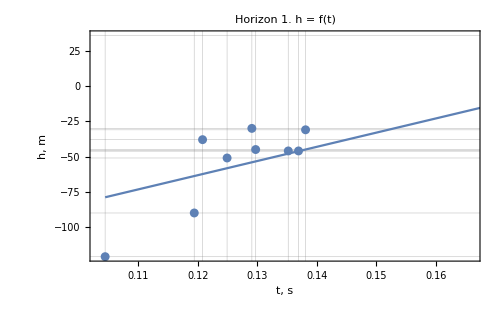
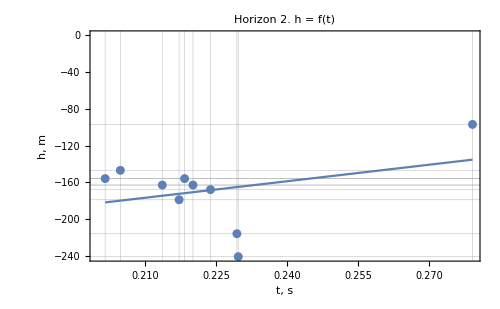
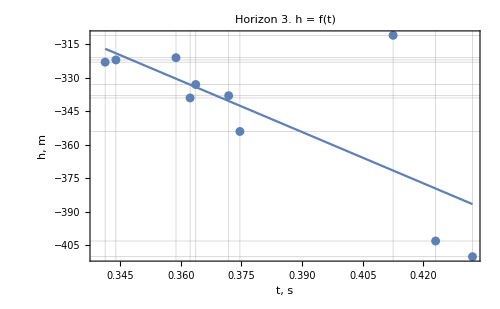

```mathematica
PlotHT[dataWellsHT,lmSetHT, t]
```

### VT

```mathematica
Clear[t]
lmSetVT=VT[datasetWells,datasetVelModel,timeNH, t][["lmSet"]]
setVT=VT[datasetWells,datasetVelModel,timeNH, t][["setVT"]]
atbt=VT[datasetWells,datasetVelModel,timeNH, t][["atbt"]]
fitParamsVT=VT[datasetWells,datasetVelModel,timeNH, t][["fitParams"]]
```

{FittedModel[2027.92-280.827 t],FittedModel[2949.12+467.215 t],FittedModel[4045.1-252.61 t]}

{{{1,0.0522251,2017},{1,0.0604008,2000},{1,0.0597041,2015},{1,0.0624604,2004},{1,0.0645368,1991},{1,0.0648577,2020},{1,0.0684548,2017},{1,0.0690456,2019},{1,0.0675948,2010},{1,0.115149,1994}},{{2,0.114849,3014},{2,0.100804,2991},{2,0.114706,2997},{2,0.108606,2981},{2,0.102407,3025},{2,0.106833,2981},{2,0.111915,2999},{2,0.109189,3024},{2,0.110071,2985},{2,0.139565,3017}},{{3,0.211507,3965},{3,0.170647,4001},{3,0.216066,4019},{3,0.187307,3989},{3,0.171974,3964},{3,0.18115,4028},{3,0.18592,4010},{3,0.181848,4033},{3,0.179405,3994},{3,0.20625,3970}}}

{{{0,0.0000789015},{5,0.0000805947},{10,0.0000806515},{15,0.0000868913},{20,0.0000849401},{25,0.0000879455},{30,0.0000927001},{35,0.0000913871},{40,0.0000921715},{45,0.0000944227},{50,0.0000944479},{55,0.000098501},{60,0.0000991259},{65,0.000105369},{70,0.000109891},{75,0.000110986},{80,0.000114998},{85,0.000116477},{90,0.000120704},{95,0.00012538},{100,0.000125059},{105,0.000124865},{110,0.000126978},{115,0.000128804},{120,0.00012974},{125,0.000127122},{130,0.000121145},{135,0.000122061},{140,0.000125003},{145,0.00011726},{150,0.000111696},{155,0.000103918},{160,0.00010395},{165,0.000102121},{170,0.0000994406},{175,0.0000996392},{180,0.000101259},{185,0.000107098},{190,0.000112247},{195,0.000115304},{200,0.000119608},{205,0.000122821},{210,0.000120552},{215,0.000126573},{220,0.000128792},{225,0.000126249},{230,0.000125262},{235,0.000126072},{240,0.000121817},{245,0.000117886},{250,0.000109377},{255,0.000104458},{260,0.0000966482},{265,0.0000924516},{270,0.0000874152},{275,0.0000815995},{280,0.000083067},{285,0.0000863738},{290,0.0000868353},{295,0.0000917797},{300,0.0000959343},{305,0.000101439},{310,0.000113065},{315,0.000118704},{320,0.000121817},{325,0.000126414},{330,0.000134978},{335,0.00014766},{340,0.000155322},{345,0.000153946},{350,0.00015661},{355,0.000164461},{360,0.00017007},{365,0.000166054},{370,0.000151987},{375,0.00014728},{380,0.000141769},{385,0.000142819},{390,0.000138448},{395,0.000131154},{400,0.000133803},{405,0.00013564},{410,0.000135098},{415,0.000136562},{420,0.000140991},{425,0.000137347},{430,0.000137486},{435,0.00013888},{440,0.00014066},{445,0.000138955},{450,0.000144619},{455,0.000139835},{460,0.000141674},{465,0.000150408},{470,0.000148892},{475,0.000152887},{480,0.000157492},{485,0.000154601},{490,0.000151505},{495,0.000153353},{500,0.000151948},{505,0.000152116},{510,0.000154049},{515,0.000148489},{520,0.000150748},{525,0.000155548},{530,0.000151123},{535,0.000147491},{540,0.000141881},{545,0.000138228},{550,0.000136862},{555,0.000131472},{560,0.000130238},{565,0.000128237},{570,0.000128334},{575,0.000131191},{580,0.000128157},{585,0.000129884},{590,0.000130294},{595,0.000126919},{600,0.000134997},{605,0.000135385},{610,0.000140936},{615,0.000142618},{620,0.000146208},{625,0.000151904},{630,0.000157379},{635,0.000164032},{640,0.000167732},{645,0.000174814},{650,0.000177689},{655,0.000187099},{660,0.000185348},{665,0.000183743},{670,0.000182618},{675,0.000180925},{680,0.000184146},{685,0.000179238},{690,0.000179538},{695,0.000178781},{700,0.000178353},{705,0.000214802},{710,0.000251223},{715,0.000276436},{720,0.000297543},{725,0.000310473},{730,0.000321065},{735,0.000314888},{740,0.000304322},{745,0.00028225},{750,0.000256851},{755,0.000228335},{760,0.000193683},{765,0.000174683},{770,0.000177782},{775,0.000182374},{780,0.000187938},{785,0.000187097},{790,0.000182329},{795,0.00018528},{800,0.000183046},{805,0.000178503},{810,0.000179381},{815,0.000174137},{820,0.000172999},{825,0.000177608},{830,0.000169517},{835,0.000170829},{840,0.000171075},{845,0.000170148},{850,0.000169757},{855,0.000166652},{860,0.000169421},{865,0.000170687},{870,0.000176618},{875,0.000171807},{880,0.000174865},{885,0.000170374},{890,0.000173091},{895,0.000168799},{900,0.000173601},{905,0.000182046},{910,0.000214192},{915,0.000239845},{920,0.000263581},{925,0.000282137},{930,0.000307605},{935,0.0003284},{940,0.000355135},{945,0.000383261},{950,0.000411469},{955,0.000448004},{960,0.000486983},{965,0.000541871},{970,0.000617804},{975,0.000711006},{980,0.000845716},{985,0.00102046},{990,0.00124848},{995,0.00153081}},{{0,-0.000959985},{5,-0.000921822},{10,-0.000890846},{15,-0.000871288},{20,-0.000803301},{25,-0.00075811},{30,-0.000733997},{35,-0.00067867},{40,-0.000639437},{45,-0.000613502},{50,-0.000576543},{55,-0.000556083},{60,-0.000534692},{65,-0.000529782},{70,-0.00053121},{75,-0.000516462},{80,-0.000526233},{85,-0.000514808},{90,-0.000527562},{95,-0.000550468},{100,-0.000561},{105,-0.000575446},{110,-0.000594732},{115,-0.00060538},{120,-0.000618526},{125,-0.000632895},{130,-0.000637873},{135,-0.000649105},{140,-0.00067654},{145,-0.000665265},{150,-0.000661759},{155,-0.000666487},{160,-0.000697654},{165,-0.000707073},{170,-0.00071997},{175,-0.000739858},{180,-0.0007802},{185,-0.000827124},{190,-0.000886562},{195,-0.000947077},{200,-0.00100461},{205,-0.0010719},{210,-0.00109881},{215,-0.00114895},{220,-0.00118337},{225,-0.00117302},{230,-0.00114332},{235,-0.0011117},{240,-0.00103269},{245,-0.000956409},{250,-0.00086669},{255,-0.000790506},{260,-0.00069911},{265,-0.000630802},{270,-0.000571325},{275,-0.000514904},{280,-0.000486965},{285,-0.000480713},{290,-0.000477974},{295,-0.000492331},{300,-0.000501247},{305,-0.000539942},{310,-0.000600782},{315,-0.000653431},{320,-0.00070185},{325,-0.000759113},{330,-0.000811791},{335,-0.00086274},{340,-0.000906503},{345,-0.000906131},{350,-0.000909096},{355,-0.000909032},{360,-0.000894851},{365,-0.000852743},{370,-0.000792275},{375,-0.000767613},{380,-0.000725735},{385,-0.000701969},{390,-0.000669749},{395,-0.000627556},{400,-0.000626862},{405,-0.000616045},{410,-0.000599088},{415,-0.000598237},{420,-0.000611343},{425,-0.000597862},{430,-0.000598062},{435,-0.000612247},{440,-0.000619848},{445,-0.000619722},{450,-0.000632411},{455,-0.000628432},{460,-0.000635254},{465,-0.0006759},{470,-0.000680578},{475,-0.000704155},{480,-0.000740554},{485,-0.000748852},{490,-0.000765912},{495,-0.000789735},{500,-0.000785301},{505,-0.000801912},{510,-0.000823217},{515,-0.00079628},{520,-0.000792982},{525,-0.000795194},{530,-0.000772674},{535,-0.000752202},{540,-0.000734588},{545,-0.000711921},{550,-0.000692532},{555,-0.000685874},{560,-0.00066778},{565,-0.000655859},{570,-0.0006534},{575,-0.000665124},{580,-0.000648024},{585,-0.000645114},{590,-0.000663428},{595,-0.000663098},{600,-0.000693894},{605,-0.000718813},{610,-0.000740305},{615,-0.00076399},{620,-0.000796858},{625,-0.000809694},{630,-0.000824546},{635,-0.000858579},{640,-0.000862121},{645,-0.000879466},{650,-0.000888288},{655,-0.000904955},{660,-0.000880293},{665,-0.000864352},{670,-0.000840136},{675,-0.000802272},{680,-0.000773727},{685,-0.000719885},{690,-0.000680269},{695,-0.000633465},{700,-0.000603902},{705,-0.000638557},{710,-0.000676945},{715,-0.000711728},{720,-0.000713971},{725,-0.000723729},{730,-0.000734875},{735,-0.000731984},{740,-0.000712357},{745,-0.000700051},{750,-0.000688332},{755,-0.000663393},{760,-0.000618469},{765,-0.000610415},{770,-0.000659807},{775,-0.000720209},{780,-0.000769049},{785,-0.000802877},{790,-0.000824938},{795,-0.000873846},{800,-0.000887463},{805,-0.000883128},{810,-0.000905354},{815,-0.000890502},{820,-0.000870034},{825,-0.000890281},{830,-0.000851449},{835,-0.000852208},{840,-0.000845096},{845,-0.000838261},{850,-0.000821485},{855,-0.000810171},{860,-0.000802789},{865,-0.00079302},{870,-0.000796185},{875,-0.000752783},{880,-0.000738108},{885,-0.000700817},{890,-0.000678831},{895,-0.000634055},{900,-0.00061227},{905,-0.000613191},{910,-0.000662533},{915,-0.00069263},{920,-0.000710386},{925,-0.000726527},{930,-0.000772558},{935,-0.000827435},{940,-0.000884594},{945,-0.000964117},{950,-0.00104358},{955,-0.00112457},{960,-0.00120961},{965,-0.00132416},{970,-0.00143845},{975,-0.00157053},{980,-0.00172273},{985,-0.00191094},{990,-0.00214349},{995,-0.00238282}},{{0,0.00236351},{5,0.00214793},{10,0.00195756},{15,0.00180373},{20,0.00163114},{25,0.00151064},{30,0.00142717},{35,0.0013239},{40,0.00123823},{45,0.00116681},{50,0.00107226},{55,0.00102964},{60,0.00094497},{65,0.00089049},{70,0.000871128},{75,0.000843045},{80,0.000870575},{85,0.000866228},{90,0.000874772},{95,0.000898504},{100,0.000896604},{105,0.000915954},{110,0.000952673},{115,0.00101948},{120,0.0010873},{125,0.00115572},{130,0.00120564},{135,0.0012413},{140,0.00126484},{145,0.00122614},{150,0.00118108},{155,0.00115961},{160,0.00118625},{165,0.00121317},{170,0.00128268},{175,0.00140737},{180,0.00155523},{185,0.00170654},{190,0.00180949},{195,0.00191942},{200,0.00204388},{205,0.00214652},{210,0.00222046},{215,0.00230636},{220,0.00245859},{225,0.00251802},{230,0.00258091},{235,0.00261893},{240,0.0025852},{245,0.00251965},{250,0.00216673},{255,0.00182262},{260,0.00146074},{265,0.00116416},{270,0.000941125},{275,0.000771704},{280,0.000701894},{285,0.000682979},{290,0.000707498},{295,0.000768423},{300,0.000852217},{305,0.000973228},{310,0.00111024},{315,0.00126305},{320,0.00140869},{325,0.00154591},{330,0.00164152},{335,0.00168409},{340,0.00169536},{345,0.00164576},{350,0.00164213},{355,0.00162175},{360,0.0015762},{365,0.00149026},{370,0.00133155},{375,0.00123108},{380,0.00113103},{385,0.00108187},{390,0.00105959},{395,0.00105142},{400,0.00107585},{405,0.00107032},{410,0.0010468},{415,0.00104071},{420,0.00104962},{425,0.00101604},{430,0.000964356},{435,0.000930001},{440,0.000915517},{445,0.000923577},{450,0.000963722},{455,0.00102321},{460,0.00112002},{465,0.00123721},{470,0.00127049},{475,0.00123306},{480,0.00121488},{485,0.00118441},{490,0.00119193},{495,0.00122501},{500,0.00127153},{505,0.00137162},{510,0.00143993},{515,0.0014412},{520,0.00147959},{525,0.00148176},{530,0.0014849},{535,0.00142745},{540,0.0013433},{545,0.00125282},{550,0.00115005},{555,0.00105161},{560,0.000969625},{565,0.000958193},{570,0.000978895},{575,0.00106088},{580,0.00116167},{585,0.00124361},{590,0.0013389},{595,0.00134509},{600,0.00131615},{605,0.00127009},{610,0.00121363},{615,0.00118867},{620,0.00120454},{625,0.00126118},{630,0.00134771},{635,0.00143687},{640,0.00152038},{645,0.00158258},{650,0.00160533},{655,0.00160132},{660,0.0015597},{665,0.00151602},{670,0.00143539},{675,0.00133485},{680,0.00124312},{685,0.00110972},{690,0.00100891},{695,0.000915282},{700,0.000851558},{705,0.000875249},{710,0.000905475},{715,0.000918856},{720,0.00089631},{725,0.000868705},{730,0.000839203},{735,0.000807426},{740,0.000795541},{745,0.00078571},{750,0.000801538},{755,0.000829763},{760,0.000859918},{765,0.000914936},{770,0.00104075},{775,0.00118757},{780,0.00132309},{785,0.00144242},{790,0.00150213},{795,0.00154731},{800,0.00156075},{805,0.00146784},{810,0.00144654},{815,0.00141316},{820,0.00141672},{825,0.00144317},{830,0.0014102},{835,0.00143673},{840,0.00144239},{845,0.00140891},{850,0.00135584},{855,0.0013015},{860,0.00131757},{865,0.00132115},{870,0.00132917},{875,0.00127407},{880,0.00124509},{885,0.00116207},{890,0.00108358},{895,0.000986909},{900,0.000930423},{905,0.000905397},{910,0.000921401},{915,0.000918723},{920,0.000905503},{925,0.000890852},{930,0.000905028},{935,0.000928519},{940,0.000985791},{945,0.0010713},{950,0.0011762},{955,0.00129138},{960,0.00141468},{965,0.00158543},{970,0.00178771},{975,0.00200302},{980,0.00219163},{985,0.00227421},{990,0.00226244},{995,0.00213005}}}

{{2027.92,-280.827},{2949.12,467.215},{4045.1,-252.61}}

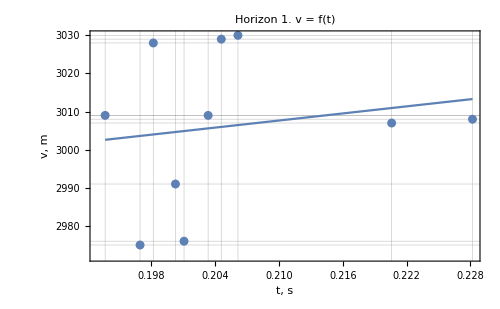
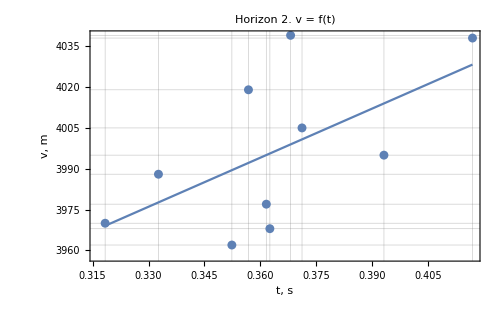

```mathematica
PlotVT[setVT,lmSetVT, t]
```

### Graphics

```mathematica
resultVT = VT[datasetWells,datasetVelModel,timeNH, t][["resultVT"]]
```

{{{0,14.},{135,80.},{245,48.},{330,77.},{470,93.},{530,85.},{650,92.},{790,102.},{840,90.},{980,185.}},{{0,-121.},{5,-108.519},{10,-96.6631},{15,-87.0814},{20,-76.6827},{25,-68.2147},{30,-60.9459},{35,-53.281},{40,-46.8375},{45,-41.4534},{50,-36.3665},{55,-32.7699},{60,-29.1832},{65,-27.2899},{70,-25.6623},{75,-23.998},{80,-23.3944},{85,-22.8676},{90,-23.2939},{95,-24.2385},{100,-24.7903},{105,-25.7629},{110,-27.4794},{115,-29.4845},{120,-31.6531},{125,-33.5293},{130,-35.0909},{135,-38.},{140,-41.4252},{145,-43.2285},{150,-45.4821},{155,-47.3887},{160,-50.7641},{165,-53.8241},{170,-56.7175},{175,-60.1226},{180,-63.7335},{185,-68.022},{190,-72.0268},{195,-75.491},{200,-78.9702},{205,-82.0357},{210,-83.9415},{215,-86.9365},{220,-88.9891},{225,-89.9351},{230,-90.7595},{235,-91.4743},{240,-90.9296},{245,-90.},{250,-87.8545},{255,-85.9316},{260,-83.087},{265,-80.5821},{270,-77.597},{275,-74.1504},{280,-72.0304},{285,-70.0984},{290,-67.3954},{295,-65.4685},{300,-63.2423},{305,-61.1658},{310,-60.0872},{315,-57.8489},{320,-55.1679},{325,-52.7518},{330,-51.},{335,-49.8883},{340,-48.0869},{345,-45.1376},{350,-42.9342},{355,-41.6303},{360,-40.1854},{365,-37.636},{370,-33.8525},{375,-31.5227},{380,-29.2341},{385,-28.0925},{390,-26.3041},{395,-24.2096},{400,-23.8266},{405,-23.4729},{410,-22.9067},{415,-22.804},{420,-23.2993},{425,-22.7137},{430,-22.8466},{435,-23.311},{440,-23.9694},{445,-24.2331},{450,-25.7322},{455,-25.7812},{460,-26.928},{465,-29.1755},{470,-30.},{475,-31.6888},{480,-33.5112},{485,-34.3234},{490,-35.1362},{495,-36.6783},{500,-37.7677},{505,-39.0826},{510,-40.6379},{515,-41.0965},{520,-42.6469},{525,-44.5088},{530,-45.},{535,-45.526},{540,-45.6681},{545,-45.9962},{550,-46.5648},{555,-46.3908},{560,-46.7476},{565,-46.8688},{570,-47.2153},{575,-47.8931},{580,-47.5264},{585,-47.8139},{590,-47.7876},{595,-47.0541},{600,-48.0396},{605,-47.7085},{610,-48.0683},{615,-47.738},{620,-47.594},{625,-47.653},{630,-47.5706},{635,-47.5425},{640,-47.0097},{645,-46.8282},{650,-46.},{655,-45.91},{660,-44.3288},{665,-42.6964},{670,-41.0713},{675,-39.3376},{680,-38.2077},{685,-36.0434},{690,-34.5547},{695,-32.9606},{700,-31.4552},{705,-34.4681},{710,-37.0818},{715,-38.3659},{720,-39.2407},{725,-39.4332},{730,-39.5365},{735,-38.3328},{740,-36.9072},{745,-34.5803},{750,-32.0208},{755,-29.1802},{760,-25.5827},{765,-23.8329},{770,-25.112},{775,-26.7828},{780,-28.7445},{785,-30.0565},{790,-31.},{795,-33.014},{800,-34.4471},{805,-35.6278},{810,-37.5192},{815,-38.611},{820,-40.1975},{825,-42.4713},{830,-42.9962},{835,-44.64},{840,-46.},{845,-47.0352},{850,-47.9454},{855,-48.2693},{860,-49.1296},{865,-49.5108},{870,-50.1973},{875,-49.1478},{880,-48.7712},{885,-47.0189},{890,-45.8051},{895,-43.2269},{900,-41.3875},{905,-39.5105},{910,-39.8859},{915,-38.6663},{920,-36.4908},{925,-33.0872},{930,-29.6023},{935,-24.9412},{940,-20.0096},{945,-14.3696},{950,-7.89576},{955,-1.14818},{960,6.36448},{965,13.847},{970,21.208},{975,28.9027},{980,36.},{985,43.058},{990,49.9917},{995,57.2185}},{{0,-241.},{5,-229.623},{10,-219.33},{15,-210.398},{20,-198.899},{25,-189.386},{30,-181.877},{35,-172.603},{40,-164.939},{45,-158.773},{50,-152.152},{55,-147.33},{60,-142.863},{65,-140.281},{70,-138.694},{75,-136.078},{80,-136.047},{85,-134.487},{90,-135.444},{95,-137.595},{100,-138.948},{105,-140.903},{110,-143.5},{115,-145.606},{120,-148.122},{125,-150.917},{130,-153.139},{135,-156.},{140,-160.217},{145,-161.591},{150,-163.643},{155,-166.393},{160,-171.167},{165,-174.321},{170,-177.724},{175,-181.598},{180,-186.823},{185,-192.328},{190,-198.428},{195,-204.322},{200,-209.762},{205,-215.472},{210,-218.674},{215,-222.903},{220,-226.028},{225,-226.564},{230,-225.816},{235,-224.658},{240,-220.508},{245,-216.},{250,-210.118},{255,-204.512},{260,-197.22},{265,-190.968},{270,-184.875},{275,-178.529},{280,-174.372},{285,-172.051},{290,-169.933},{295,-169.314},{300,-168.08},{305,-169.421},{310,-172.377},{315,-174.334},{320,-175.745},{325,-177.616},{330,-179.},{335,-180.16},{340,-180.802},{345,-178.731},{350,-176.96},{355,-175.106},{360,-172.477},{365,-168.157},{370,-162.616},{375,-159.5},{380,-155.225},{385,-152.289},{390,-148.783},{395,-144.521},{400,-143.589},{405,-141.959},{410,-139.929},{415,-139.315},{420,-139.947},{425,-138.53},{430,-138.339},{435,-139.396},{440,-140.025},{445,-140.147},{450,-141.398},{455,-141.428},{460,-142.403},{465,-146.055},{470,-147.},{475,-149.408},{480,-152.749},{485,-154.092},{490,-156.078},{495,-158.533},{500,-159.063},{505,-161.03},{510,-163.291},{515,-162.31},{520,-162.889},{525,-163.811},{530,-163.},{535,-162.253},{540,-161.625},{545,-160.541},{550,-159.586},{555,-159.477},{560,-158.414},{565,-157.722},{570,-157.673},{575,-158.638},{580,-157.315},{585,-157.011},{590,-158.279},{595,-158.046},{600,-160.096},{605,-161.597},{610,-162.759},{615,-163.992},{620,-165.768},{625,-166.105},{630,-166.525},{635,-168.139},{640,-167.722},{645,-168.151},{650,-168.},{655,-168.308},{660,-165.998},{665,-164.203},{670,-161.844},{675,-158.536},{680,-155.797},{685,-151.208},{690,-147.52},{695,-143.177},{700,-140.1},{705,-142.195},{710,-144.52},{715,-146.525},{720,-146.173},{725,-146.432},{730,-146.857},{735,-146.355},{740,-144.729},{745,-143.714},{750,-142.833},{755,-141.048},{760,-137.748},{765,-137.433},{770,-141.759},{775,-146.789},{780,-150.852},{785,-153.825},{790,-156.},{795,-159.902},{800,-161.5},{805,-161.953},{810,-164.051},{815,-163.783},{820,-163.09},{825,-164.905},{830,-162.866},{835,-163.25},{840,-163.},{845,-162.627},{850,-161.438},{855,-160.43},{860,-159.492},{865,-158.184},{870,-157.531},{875,-153.43},{880,-151.033},{885,-146.702},{890,-143.149},{895,-137.484},{900,-133.211},{905,-130.412},{910,-131.059},{915,-129.735},{920,-127.066},{925,-123.857},{930,-122.307},{935,-120.785},{940,-118.797},{945,-117.533},{950,-115.524},{955,-112.872},{960,-109.703},{965,-107.239},{970,-103.897},{975,-100.487},{980,-97.},{985,-93.9313},{990,-91.3556},{995,-87.7841}},{{0,-403.},{5,-390.257},{10,-378.252},{15,-367.986},{20,-355.619},{25,-346.507},{30,-339.955},{35,-331.359},{40,-323.875},{45,-317.357},{50,-308.201},{55,-303.935},{60,-294.954},{65,-288.88},{70,-286.66},{75,-283.348},{80,-286.546},{85,-285.978},{90,-286.887},{95,-289.509},{100,-289.169},{105,-291.217},{110,-295.133},{115,-302.109},{120,-308.867},{125,-315.387},{130,-319.914},{135,-323.},{140,-324.922},{145,-321.154},{150,-316.704},{155,-314.422},{160,-316.725},{165,-319.017},{170,-325.138},{175,-335.749},{180,-347.576},{185,-358.919},{190,-366.19},{195,-373.668},{200,-381.825},{205,-388.28},{210,-392.766},{215,-397.89},{220,-406.783},{225,-410.098},{230,-413.575},{235,-415.638},{240,-413.719},{245,-410.},{250,-388.852},{255,-365.891},{260,-338.362},{265,-312.162},{270,-289.347},{275,-269.475},{280,-260.487},{285,-258.024},{290,-261.447},{295,-269.476},{300,-279.819},{305,-293.578},{310,-307.829},{315,-322.388},{320,-335.209},{325,-346.502},{330,-354.},{335,-357.279},{340,-358.175},{345,-354.489},{350,-354.235},{355,-352.684},{360,-349.146},{365,-342.276},{370,-328.87},{375,-319.794},{380,-310.24},{385,-305.296},{390,-302.958},{395,-302.034},{400,-304.426},{405,-303.77},{410,-301.274},{415,-300.55},{420,-301.372},{425,-297.798},{430,-292.197},{435,-288.341},{440,-286.649},{445,-287.491},{450,-291.862},{455,-298.152},{460,-307.912},{465,-319.005},{470,-322.},{475,-318.547},{480,-316.82},{485,-313.909},{490,-314.558},{495,-317.571},{500,-321.731},{505,-330.427},{510,-336.063},{515,-336.019},{520,-339.002},{525,-338.976},{530,-339.},{535,-334.002},{540,-326.533},{545,-318.144},{550,-308.131},{555,-297.927},{560,-288.842},{565,-287.113},{570,-288.842},{575,-296.887},{580,-306.294},{585,-313.411},{590,-321.358},{595,-321.333},{600,-318.243},{605,-313.588},{610,-307.882},{615,-305.035},{620,-306.047},{625,-310.818},{630,-318.085},{635,-325.292},{640,-331.788},{645,-336.438},{650,-338.},{655,-337.554},{660,-334.242},{665,-330.774},{670,-324.252},{675,-315.803},{680,-307.766},{685,-295.287},{690,-285.247},{695,-275.332},{700,-268.288},{705,-271.37},{710,-275.155},{715,-276.988},{720,-274.759},{725,-271.888},{730,-268.707},{735,-265.142},{740,-263.924},{745,-262.91},{750,-265.033},{755,-268.577},{760,-272.215},{765,-278.531},{770,-292.014},{775,-306.371},{780,-318.518},{785,-328.441},{790,-333.},{795,-336.217},{800,-336.816},{805,-328.828},{810,-326.473},{815,-323.018},{820,-322.572},{825,-323.961},{830,-320.317},{835,-321.571},{840,-321.},{845,-317.084},{850,-311.361},{855,-305.325},{860,-305.394},{865,-304.275},{870,-303.463},{875,-296.972},{880,-292.66},{885,-283.123},{890,-273.574},{895,-261.623},{900,-253.442},{905,-248.523},{910,-248.127},{915,-245.539},{920,-241.67},{925,-237.532},{930,-236.585},{935,-236.569},{940,-240.071},{945,-246.124},{950,-253.47},{955,-261.041},{960,-268.581},{965,-279.147},{970,-290.926},{975,-302.365},{980,-311.},{985,-312.47},{990,-308.008},{995,-295.882}}}

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[horNH,  GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
						PlotLabel -> "Depth Section"]
```

-Graphics-

{{{35,82.},{280,97.},{400,71.},{485,67.},{555,73.},{645,65.},{710,53.},{765,64.},{945,63.},{1000,22.}},{{0,-34.332},{5,-34.3904},{10,-34.7456},{15,-35.7729},{20,-34.6209},{25,-34.896},{30,-34.7445},{35,-35.8876},{40,-37.1569},{45,-37.1956},{50,-37.9605},{55,-40.0634},{60,-41.7204},{65,-42.9419},{70,-43.1215},{75,-44.7974},{80,-47.0713},{85,-46.8511},{90,-47.2137},{95,-47.5546},{100,-49.2527},{105,-49.7694},{110,-49.02},{115,-47.6565},{120,-48.4376},{125,-48.7332},{130,-48.8048},{135,-47.2943},{140,-43.5566},{145,-37.0925},{150,-31.5756},{155,-30.5528},{160,-28.4076},{165,-27.3821},{170,-29.5773},{175,-30.8264},{180,-32.0399},{185,-35.2389},{190,-36.8388},{195,-35.759},{200,-34.6399},{205,-35.1007},{210,-33.9685},{215,-33.4073},{220,-33.8948},{225,-35.4616},{230,-37.5505},{235,-38.024},{240,-38.4771},{245,-42.1393},{250,-42.1289},{255,-43.3044},{260,-43.8248},{265,-44.1978},{270,-44.6947},{275,-45.1141},{280,-44.2927},{285,-44.3752},{290,-45.9732},{295,-46.9496},{300,-46.725},{305,-46.5991},{310,-48.5975},{315,-49.6971},{320,-50.1222},{325,-49.3134},{330,-48.1485},{335,-47.9336},{340,-50.109},{345,-49.7118},{350,-50.0609},{355,-50.145},{360,-49.9178},{365,-51.6815},{370,-51.6467},{375,-51.0923},{380,-49.6697},{385,-51.9016},{390,-53.7769},{395,-54.5198},{400,-55.5921},{405,-56.8551},{410,-58.1537},{415,-59.4732},{420,-58.9851},{425,-58.9549},{430,-59.4923},{435,-59.5673},{440,-58.2831},{445,-58.3268},{450,-57.7453},{455,-57.0029},{460,-58.0382},{465,-56.2152},{470,-55.0909},{475,-55.7545},{480,-55.6833},{485,-55.6688},{490,-54.8747},{495,-52.5062},{500,-53.0374},{505,-54.715},{510,-55.0019},{515,-52.8276},{520,-55.2954},{525,-55.2463},{530,-56.727},{535,-57.405},{540,-57.3168},{545,-56.8004},{550,-57.5805},{555,-57.9748},{560,-60.3133},{565,-59.5252},{570,-58.923},{575,-58.3403},{580,-58.2627},{585,-57.5803},{590,-57.1378},{595,-55.7053},{600,-56.2758},{605,-56.5168},{610,-55.9184},{615,-57.2047},{620,-58.8232},{625,-58.1301},{630,-58.7245},{635,-57.4112},{640,-57.1304},{645,-57.175},{650,-57.1324},{655,-58.5808},{660,-58.0729},{665,-59.2141},{670,-62.2981},{675,-65.0064},{680,-65.4248},{685,-65.8381},{690,-68.2435},{695,-67.2368},{700,-66.6216},{705,-65.1968},{710,-63.9903},{715,-63.6045},{720,-63.3634},{725,-59.9408},{730,-60.1631},{735,-58.4103},{740,-56.6316},{745,-54.8451},{750,-51.8685},{755,-51.1601},{760,-49.6001},{765,-48.4202},{770,-48.8691},{775,-48.79},{780,-50.3801},{785,-52.0239},{790,-52.689},{795,-54.3971},{800,-54.7101},{805,-53.3338},{810,-53.6049},{815,-53.3025},{820,-53.463},{825,-51.5262},{830,-51.0925},{835,-47.8028},{840,-47.7387},{845,-49.9943},{850,-51.0996},{855,-50.5828},{860,-49.4164},{865,-45.6339},{870,-46.609},{875,-44.2325},{880,-42.9554},{885,-43.8847},{890,-43.6346},{895,-43.9353},{900,-47.0768},{905,-47.8617},{910,-49.9368},{915,-50.728},{920,-52.1864},{925,-53.629},{930,-55.0548},{935,-57.2416},{940,-58.5908},{945,-60.7372},{950,-63.9178},{955,-67.891},{960,-69.2182},{965,-72.3449},{970,-73.0398},{975,-74.8075},{980,-77.5787},{985,-78.0611},{990,-78.1373},{995,-79.7455}},{{0,-159.647},{5,-167.734},{10,-174.971},{15,-179.77},{20,-186.778},{25,-191.408},{30,-195.208},{35,-196.865},{40,-197.629},{45,-198.643},{50,-198.603},{55,-196.203},{60,-193.761},{65,-190.695},{70,-188.915},{75,-185.141},{80,-179.914},{85,-177.693},{90,-174.592},{95,-170.226},{100,-166.297},{105,-163.809},{110,-160.787},{115,-158.005},{120,-154.398},{125,-151.104},{130,-147.15},{135,-145.138},{140,-145.787},{145,-150.924},{150,-154.902},{155,-155.174},{160,-157.945},{165,-159.003},{170,-159.008},{175,-159.994},{180,-160.972},{185,-159.447},{190,-159.496},{195,-162.794},{200,-165.001},{205,-165.151},{210,-166.086},{215,-167.014},{220,-167.023},{225,-165.047},{230,-162.707},{235,-161.498},{240,-161.622},{245,-157.778},{250,-157.909},{255,-157.846},{260,-156.823},{265,-157.07},{270,-157.346},{275,-157.194},{280,-159.059},{285,-159.676},{290,-160.265},{295,-161.578},{300,-162.764},{305,-163.617},{310,-163.704},{315,-164.155},{320,-163.653},{325,-165.557},{330,-167.211},{335,-167.072},{340,-166.22},{345,-168.342},{350,-169.229},{355,-169.776},{360,-172.217},{365,-171.605},{370,-172.134},{375,-174.305},{380,-174.484},{385,-171.47},{390,-169.466},{395,-168.334},{400,-166.294},{405,-164.222},{410,-161.929},{415,-160.452},{420,-159.106},{425,-158.692},{430,-156.076},{435,-157.658},{440,-160.328},{445,-160.309},{450,-161.548},{455,-165.906},{460,-166.564},{465,-168.031},{470,-172.213},{475,-173.342},{480,-172.798},{485,-172.724},{490,-173.848},{495,-175.677},{500,-173.356},{505,-170.916},{510,-171.03},{515,-170.482},{520,-165.459},{525,-164.96},{530,-163.862},{535,-162.98},{540,-160.908},{545,-160.664},{550,-161.773},{555,-162.651},{560,-158.6},{565,-158.341},{570,-158.803},{575,-157.835},{580,-157.413},{585,-158.418},{590,-159.11},{595,-160.801},{600,-160.762},{605,-161.751},{610,-164.86},{615,-165.109},{620,-166.639},{625,-167.711},{630,-167.845},{635,-169.989},{640,-170.589},{645,-171.012},{650,-170.923},{655,-168.685},{660,-167.851},{665,-167.091},{670,-165.617},{675,-163.801},{680,-164.128},{685,-163.04},{690,-159.89},{695,-160.817},{700,-161.545},{705,-163.22},{710,-167.178},{715,-167.789},{720,-169.876},{725,-175.12},{730,-178.656},{735,-183.734},{740,-187.072},{745,-188.447},{750,-190.212},{755,-189.41},{760,-188.641},{765,-188.543},{770,-186.088},{775,-183.616},{780,-177.951},{785,-172.559},{790,-168.835},{795,-162.295},{800,-156.639},{805,-152.533},{810,-146.424},{815,-142.034},{820,-139.698},{825,-139.486},{830,-138.594},{835,-143.223},{840,-143.421},{845,-143.241},{850,-143.329},{855,-145.675},{860,-148.914},{865,-153.359},{870,-153.828},{875,-157.079},{880,-158.846},{885,-158.338},{890,-161.765},{895,-163.64},{900,-162.851},{905,-165.572},{910,-165.65},{915,-167.109},{920,-168.3},{925,-167.9},{930,-167.677},{935,-166.607},{940,-165.266},{945,-164.016},{950,-161.644},{955,-159.592},{960,-159.837},{965,-157.55},{970,-159.276},{975,-158.808},{980,-158.575},{985,-160.506},{990,-163.239},{995,-163.588}},{{0,-284.352},{5,-303.75},{10,-320.759},{15,-335.752},{20,-350.844},{25,-362.155},{30,-372.877},{35,-378.504},{40,-378.098},{45,-375.565},{50,-368.575},{55,-358.642},{60,-348.942},{65,-340.827},{70,-336.523},{75,-334.242},{80,-332.596},{85,-333.832},{90,-333.12},{95,-331.308},{100,-325.64},{105,-319.152},{110,-310.54},{115,-299.355},{120,-287.724},{125,-277.64},{130,-269.398},{135,-264.754},{140,-263.474},{145,-268.124},{150,-273.588},{155,-274.733},{160,-276.74},{165,-277.36},{170,-280.529},{175,-284.262},{180,-288.402},{185,-289.466},{190,-292.356},{195,-297.766},{200,-301.291},{205,-301.415},{210,-303.776},{215,-307.56},{220,-308.676},{225,-305.236},{230,-299.745},{235,-293.252},{240,-288.566},{245,-282.237},{250,-280.474},{255,-282.225},{260,-286.571},{265,-292.582},{270,-297.28},{275,-301.158},{280,-304.418},{285,-303.914},{290,-301.951},{295,-299.621},{300,-297.72},{305,-298.042},{310,-297.163},{315,-300.516},{320,-306.429},{325,-314.788},{330,-322.835},{335,-325.954},{340,-325.036},{345,-322.257},{350,-318.138},{355,-314.117},{360,-313.761},{365,-314.564},{370,-316.108},{375,-320.167},{380,-324.9},{385,-329.196},{390,-334.011},{395,-336.393},{400,-338.09},{405,-332.064},{410,-322.781},{415,-311.314},{420,-299.893},{425,-292.59},{430,-286.83},{435,-290.22},{440,-296.571},{445,-301.954},{450,-307.517},{455,-313.164},{460,-320.463},{465,-329.359},{470,-339.96},{475,-347.497},{480,-353.216},{485,-353.696},{490,-345.617},{495,-334.725},{500,-321.941},{505,-312.023},{510,-309.638},{515,-309.15},{520,-309.078},{525,-312.753},{530,-314.295},{535,-315.806},{540,-315.366},{545,-316.335},{550,-317.216},{555,-318.583},{560,-313.263},{565,-310.46},{570,-307.257},{575,-303.292},{580,-301.936},{585,-300.246},{590,-298.827},{595,-302.978},{600,-304.426},{605,-305.216},{610,-308.664},{615,-311.875},{620,-319.006},{625,-326.883},{630,-331.902},{635,-337.983},{640,-340.654},{645,-342.501},{650,-338.083},{655,-332.254},{660,-326.444},{665,-318.444},{670,-310.214},{675,-303.598},{680,-303.372},{685,-306.974},{690,-309.128},{695,-320.135},{700,-330.467},{705,-340.787},{710,-348.189},{715,-346.644},{720,-342.965},{725,-337.402},{730,-328.773},{735,-326.251},{740,-328.157},{745,-338.633},{750,-355.67},{755,-372.06},{760,-389.174},{765,-402.038},{770,-391.515},{775,-372.845},{780,-352.064},{785,-330.313},{790,-311.234},{795,-293.454},{800,-279.795},{805,-272.777},{810,-267.303},{815,-265.599},{820,-266.363},{825,-268.491},{830,-268.697},{835,-270.938},{840,-269.7},{845,-267.679},{850,-268.217},{855,-271.374},{860,-278.479},{865,-286.827},{870,-291.093},{875,-297.415},{880,-301.158},{885,-302.285},{890,-304.371},{895,-303.532},{900,-299.294},{905,-299.876},{910,-298.921},{915,-302.175},{920,-308.172},{925,-314.875},{930,-326.364},{935,-338.464},{940,-343.712},{945,-347.248},{950,-336.819},{955,-323.598},{960,-312.383},{965,-300.999},{970,-296.14},{975,-296.08},{980,-301.46},{985,-312.473},{990,-326.883},{995,-341.119}}}

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
Show[ListLinePlot[horNH, GridLines->{DeleteDuplicates[Normal[datasetWells[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horNH]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->Blue],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->Red]
]
```

-Graphics-